# Anyonica

## Installing the Package

Locate the paclet file (with the .paclet extension) and evaluate PacletInstall on the path to this file

```mathematica
PacletInstall["path_To_Paclet"]
```

## Loading the Package

To load the package use the following command

```mathematica
<<Anyonica`
```

Note: the first time you load any of the packages it might take some time. This is because the packages create data files that are optimized for import later on. The next time you load the package should be much faster!

## All Functions

The following command returns a list of all functions that the package provides:

```mathematica
?Anyonica`*
```

Click on the function names or invoke ?<FunctionName> to get extra info on the usage of a function
Note: at this moment invoking ?FusionRing gives some errors about formatting. This will be sorted out but is of low priority at the moment since the correct output is returned as well

```mathematica
?WhichDecompositions
```

```mathematica
?EquivalentFusionRingsQ
```

```mathematica
?FusionRing
```

FusionRing::elnotfound: StandardForm[Short[Shallow[HoldForm[Anyonica`Elements`PackagePrivate`el], {10, 50}], 5]] is not a known name of an element

## Initializing a FusionRing Object

### From a Multiplication Table

Initialize your own fusion ring by calling FusionRing with the option “Multiplicationtable” → table.

```mathematica
myring = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}}
]
```

FusionRing[3,1,0,_]

The format of the table is such that table[[a, b, c]] returns 𝒩_(a,b)^c, with 𝒩_(a,b)^c  the structure constants of the ring, i.e. those integers for which a×b = ∑_c 𝒩_(a,b)^c  c. The multiplication table is automatically checked for errors and specific error messages have been implemented.

Give a fusion ring one or multiple names

```mathematica
myring = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"Names" -> {"Ising","SU(2)_2"}
]
```

FusionRing[Ising]

The format of the "Names" option is a list of strings that contains the names by which this ring is known. Once a name is known the format of a fusion ring simplifies to FusionRing["name"] where "name" is the first element of the provided list of strings.

Give all the elements an indexed name  (bugged atm :( )

```mathematica
myring = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"ElementsName"-> "τ"
];
myring // ElementNames
```

{𝟭,𝟮,𝟯}

The default names for the elements are bold unicode numbers

```mathematica
FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}}
] // ElementNames
```

{𝟭,𝟮,𝟯}

Give each element its own name

```mathematica
myring = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"ElementNames"-> {"1","ψ","σ"}
];
myring // ElementNames
```

{1,ψ,σ}

### From the Built-In List of Fusion Rings

Access the built-in list of fusion rings

```mathematica
FusionRingList
```

or use the shorthand

```mathematica
FRL
```

You can refer to certain rings for later use

```mathematica
ring1 = FusionRingList[[4]]
```

FusionRing[Ising]

### Via Known Constructions

Generate the fusion ring ℤ_n for n=3

```mathematica
z3 = FusionRingZn[ 3 ]
```

FusionRing[ℤ_3]

Show its multiplication table (with “fancy” formatting)

```mathematica
z3 // SymbolicMultiplicationTable // TableForm
```

𝟭 | 𝟮 | 𝟯
𝟮 | 𝟯 | 𝟭
𝟯 | 𝟭 | 𝟮

Generate the fusion ring (SU(2))_k for k=5

```mathematica
su2k5 = FusionRingSU2k[ 5 ]
```

FusionRing[SU(2)_5]

```mathematica
su2k5 // SymbolicMultiplicationTable // TableForm
```

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭+𝟯 | 𝟮+𝟰 | 𝟯+𝟱 | 𝟰+𝟲 | 𝟱
𝟯 | 𝟮+𝟰 | 𝟭+𝟯+𝟱 | 𝟮+𝟰+𝟲 | 𝟯+𝟱 | 𝟰
𝟰 | 𝟯+𝟱 | 𝟮+𝟰+𝟲 | 𝟭+𝟯+𝟱 | 𝟮+𝟰 | 𝟯
𝟱 | 𝟰+𝟲 | 𝟯+𝟱 | 𝟮+𝟰 | 𝟭+𝟯 | 𝟮
𝟲 | 𝟱 | 𝟰 | 𝟯 | 𝟮 | 𝟭

Note that the order in which the elements appear differ from the same ring in the FusionRingList

```mathematica
(* Find the equivalent ring in the built in list using FirstCase[ <list>, <pattern> /; <condition> ] *)
su2k5FromList = FirstCase[ FRL, ring_ /; EquivalentFusionRingsQ[ ring, su2k5 ] ];
su2k5FromList // SymbolicMultiplicationTable // TableForm
```

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭 | 𝟲 | 𝟱 | 𝟰 | 𝟯
𝟯 | 𝟲 | 𝟭+𝟯+𝟰 | 𝟯+𝟰 | 𝟱+𝟲 | 𝟮+𝟱+𝟲
𝟰 | 𝟱 | 𝟯+𝟰 | 𝟭+𝟯 | 𝟮+𝟲 | 𝟱+𝟲
𝟱 | 𝟰 | 𝟱+𝟲 | 𝟮+𝟲 | 𝟭+𝟯 | 𝟯+𝟰
𝟲 | 𝟯 | 𝟮+𝟱+𝟲 | 𝟱+𝟲 | 𝟯+𝟰 | 𝟭+𝟯+𝟰

The reason for this behaviour is that for a generic ring (from the FusionRingList) there is no canonical order of the particles, while the fusion ring constructed using FusionRingSU2k is built with representation theory in mind.

Generate the fusion ring (PSU(2))_k for k=4

```mathematica
FusionRingPSU2k[ 4 ]
```

FusionRing[PSU(2)_4]

Generate the Haagerup-Izumi ring obtained from ℤ_3

```mathematica
FusionRingHI[ CyclicGroup[3] ]
```

FusionRing[6,1,2,_]

Any Abelian group with available multiplication table built into Mathematica (see  guide/GroupTheory in the documentation centre) can be used

```mathematica
FusionRingHI[ AlternatingGroup[3] ]
```

FusionRing[6,1,2,_]

Generate a fusion ring from a built-in group whose multiplication table is available

```mathematica
FusionRingFromGroup[ DihedralGroup[ 3 ] ]
```

FusionRing[D_3]

```mathematica
FusionRingFromGroup[ AlternatingGroup[ 4 ] ]
```

FusionRing[A_4]

## Properties of Fusion Rings

The full structure of a FusionRing object is rather involved:

```mathematica
FusionRingList[[17]] // FullForm
```

FusionRing[Association[Rule["Barcode",9520970329946264247],Rule["DirectProductDecompositions",Hold[List[]]],Rule["Dual",Association[Rule[1,1],Rule[2,2],Rule[3,4],Rule[4,3]]],Rule["ElementNames",List["\|01D7ED","\|01D7EE","\|01D7EF","\|01D7F0"]],Rule["ElementsName",None],Rule["FormalParameters",List[4,1,2,4]],Rule["MultiplicationTable",List[List[List[1,0,0,0],List[0,1,0,0],List[0,0,1,0],List[0,0,0,1]],List[List[0,1,0,0],List[1,0,0,0],List[0,0,0,1],List[0,0,1,0]],List[List[0,0,1,0],List[0,0,0,1],List[0,1,1,1],List[1,0,1,1]],List[List[0,0,0,1],List[0,0,1,0],List[1,0,1,1],List[0,1,1,1]]]],Rule["Names",List["Pseudo PSU(2)_6","[I ⊴ ℤ_2]"]],Rule["SubFusionRings",Hold[List[List[List[1,2],FRBC[List[2,1,0,1]]]]]],Rule["QuantumDimensions",List[1,1,Plus[1,Power[2,Rational[1,2]]],Plus[1,Power[2,Rational[1,2]]]]],Rule["SMatrices",List[]],Rule["TwistFactors",List[List[0,0,0,0],List[0,0,Rational[1,2],Rational[1,2]]]],Rule["ModularData",List[]],Rule["Characters",List[List[1,1,Plus[1,Power[2,Rational[1,2]]],Plus[1,Power[2,Rational[1,2]]]],List[1,1,Plus[1,Times[-1,Power[2,Rational[1,2]]]],Plus[1,Times[-1,Power[2,Rational[1,2]]]]],List[1,-1,Complex[0,1],Complex[0,-1]],List[1,-1,Complex[0,-1],Complex[0,1]]]]]]

To get information about the various properties several functions (and their abbreviations consisting of just the capitalized letters) have been implemented.

Get the amount of generators of a fusion ring

```mathematica
r = FusionRingList[[15]];
Rank[ r ]
```

4

Get the multiplication table of a fusion ring

```mathematica
MultiplicationTable[ r ] (* or MT[ r ] *)
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{0,1,0,0},{1,0,1,1},{0,1,0,0},{0,1,0,0}},{{0,0,1,0},{0,1,0,0},{0,0,0,1},{1,0,0,0}},{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,0,1,0}}}

Get the common names of a fusion ring

```mathematica
Names[ r ]
```

{Potts,TY(ℤ_3),[ℤ_3 ⊴ ℤ_3]}

Get the names of  the elements of a fusion ring

```mathematica
ElementNames[ r ]
```

{𝟭,𝟮,𝟯,𝟰}

Get the symbolic multiplication table of a fusion ring

```mathematica
SymbolicMultiplicationTable[ r ] (* or SMT[ r ] *)
```

{{𝟭,𝟮,𝟯,𝟰},{𝟮,𝟭+𝟯+𝟰,𝟮,𝟮},{𝟯,𝟮,𝟰,𝟭},{𝟰,𝟮,𝟭,𝟯}}

Use TableForm to get a nice overview

```mathematica
TableForm[ SMT[ r ] ]
```

𝟭 | 𝟮 | 𝟯 | 𝟰
𝟮 | 𝟭+𝟯+𝟰 | 𝟮 | 𝟮
𝟯 | 𝟮 | 𝟰 | 𝟭
𝟰 | 𝟮 | 𝟭 | 𝟯

Get the matrix that sends each particle to its antiparticle

```mathematica
AntiparticleMatrix[ r ] (* or AM[ r ] *)
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

It is clear that the first two particles are self dual and the last two are each others antiparticle

```mathematica
MatrixForm[ AM[ r ] ]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

Find the multiplicity  of a fusion ring

```mathematica
Multiplicity[ r ] (* Or Mult[ r ] *)
```

1

Check whether a fusion ring is commutative

```mathematica
CommutativeQ[ r ] (* Or CQ[ r ] *)
```

True

Check whether a fusion ring comes from a group

```mathematica
GroupRingQ[ r ] (* Or GQ[ r ] *)
```

False

Get the indices of the non-zero structure constants 𝒩_(a,b)^c ≠ 0

```mathematica
NonZeroStructureConstants[ r ] (* or NZSC[ r ] *)
```

{{1,1,1},{1,2,2},{1,3,3},{1,4,4},{2,1,2},{2,2,1},{2,2,3},{2,2,4},{2,3,2},{2,4,2},{3,1,3},{3,2,2},{3,3,4},{3,4,1},{4,1,4},{4,2,2},{4,3,1},{4,4,3}}

Get the amount of nonzero structure constants

```mathematica
NNonZeroStructureConstants[ r ] (* or NNZSC[ r ] *)
```

18

Get a tuple with the amount of self-dual and non-self-dual particles

```mathematica
NSelfDualNonSelfDual[ r ] (* or NSDNSD[ r ] *)
```

{2,2}

Functions for each number separately are also available

```mathematica
{ NSelfDual[ r ], NNonSelfDual[ r ] } (* or { NSD[ r ], NNSD[ r ] } *)
```

{2,2}

Get the quantum dimensions of the particles, in the same order as the particles

```mathematica
QuantumDimensions[ r ] (* or QD[ r ] *)
```

{1,√3,1,1}

Get the square of the total quantum dimension

```mathematica
TotalQuantumDimensionSquared[ r ] (* or TQDS[ r ] *)
```

6

Get the formal code of the fusion ring

```mathematica
FormalCode[ r ] (* or FC[ r ] *)
```

{4,1,2,2}

This code can then be used to quickly  search for the fusion ring in the database

```mathematica
FusionRingByCode[{4,1,2,2}]
```

FusionRing[Potts]

To get the (generalized) S-matrices of a fusion ring, evaluate

```mathematica
r = FRL[[20]];
SMatrices[ r ] (* or SM[ r ] *)
```

{{{1/(2 √3),1/(2 √3),1/(√3),1/2,1/2},{1/(2 √3),1/(2 √3),1/(√3),-1/2,-1/2},{1/(√3),1/(√3),-1/(√3),0,0},{1/2,-1/2,0,1/2,-1/2},{1/2,-1/2,0,-1/2,1/2}},{{1/(2 √3),1/(2 √3),1/(√3),1/2,1/2},{1/(2 √3),1/(2 √3),1/(√3),-1/2,-1/2},{1/(√3),1/(√3),-1/(√3),0,0},{1/2,-1/2,0,-1/2,1/2},{1/2,-1/2,0,1/2,-1/2}},{{1/(2 √3),1/(2 √3),1/(√3),-1/2,-1/2},{1/(2 √3),1/(2 √3),1/(√3),1/2,1/2},{1/(√3),1/(√3),-1/(√3),0,0},{-1/2,1/2,0,-1/2,1/2},{-1/2,1/2,0,1/2,-1/2}},{{1/(2 √3),1/(2 √3),1/(√3),-1/2,-1/2},{1/(2 √3),1/(2 √3),1/(√3),1/2,1/2},{1/(√3),1/(√3),-1/(√3),0,0},{-1/2,1/2,0,1/2,-1/2},{-1/2,1/2,0,-1/2,1/2}}}

Note: some of the S-matrices do not have the quantum dimensions of the fusion ring as first row. The term “generalized S-matrices” might be more adequate but to keep things short we just call them S-matrices as well.

or a bit more tidy

```mathematica
MatrixForm /@ SMatrices[ r ]
```

{(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | 1/2 | -1/2
1/2 | -1/2 | 0 | -1/2 | 1/2),(1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
1/2 | -1/2 | 0 | -1/2 | 1/2
1/2 | -1/2 | 0 | 1/2 | -1/2),(1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
-1/2 | 1/2 | 0 | -1/2 | 1/2
-1/2 | 1/2 | 0 | 1/2 | -1/2),(1/(2 √3) | 1/(2 √3) | 1/(√3) | -1/2 | -1/2
1/(2 √3) | 1/(2 √3) | 1/(√3) | 1/2 | 1/2
1/(√3) | 1/(√3) | -1/(√3) | 0 | 0
-1/2 | 1/2 | 0 | 1/2 | -1/2
-1/2 | 1/2 | 0 | -1/2 | 1/2)}

Note: functions such as TableForm and MatrixForm don’t just display the results nicely, they actually create formatted objects that can not be used as matrices in the usual sense! You might want to use these functions only after you’re done calculating and/or assigning values.

Getting the twist factors α_i (for which T_(i i) = e^(2 π α_i  ⅈ) )

```mathematica
TwistFactors[ r ] (* or TA[ r ] *)
```

{{0,0,0,0,0},{0,0,1/3,-1/8,3/8},{0,0,-1/3,-1/4,-1/4},{0,0,0,-3/8,1/8},{0,0,1/3,1/2,1/2},{0,0,-1/3,3/8,-1/8},{0,0,0,1/4,1/4},{0,0,1/3,1/8,-3/8},{0,0,-1/3,0,0},{0,0,0,-1/8,3/8},{0,0,1/3,-1/4,-1/4},{0,0,-1/3,-3/8,1/8},{0,0,0,1/2,1/2},{0,0,-1/3,1/4,1/4},{0,0,1/3,0,0},{0,0,0,-1/4,-1/4},{0,0,-1/3,1/2,1/2},{0,0,1/3,1/4,1/4}}

To get the (generalized) T-matrices one can invoke

```mathematica
tMatrices = DiagonalMatrix[ Exp[ 2 π ⅈ  # ] ]& /@ TF[ r ];
MatrixForm /@ tMatrices
```

{(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^((3 ⅈ π)/4)),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | ⅇ^(-(3 ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ π)/4)),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^((3 ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^(-(ⅈ π)/4)),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^(-(3 ⅈ π)/4)),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^((3 ⅈ π)/4)),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅇ^(-(3 ⅈ π)/4) | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ π)/4)),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | ⅈ)}

Note:  the T-matrices might not match with any S-matrix in the sense that there might not exist a λ for which (S.T)^3 = λ S^2. The term “generalized T-matrix” would be more adequate but to keep things short we just call them T-matrices.

Getting matching pairs of S and T matrices (i.e. matrices for which there exists a λ for which (S.T)^3 = λ S^2)

```mathematica
ModularData[ r ] (* or MD[ r ] *)
```

{<|SMatrix→{{1/(2 √3),1/(2 √3),1/(√3),1/2,1/2},{1/(2 √3),1/(2 √3),1/(√3),-1/2,-1/2},{1/(√3),1/(√3),-1/(√3),0,0},{1/2,-1/2,0,1/2,-1/2},{1/2,-1/2,0,-1/2,1/2}},TwistFactors→{{0,0,-1/3,3/8,-1/8},{0,0,-1/3,-1/8,3/8},{0,0,1/3,1/8,-3/8},{0,0,1/3,-3/8,1/8}}|>,<|SMatrix→{{1/(2 √3),1/(2 √3),1/(√3),1/2,1/2},{1/(2 √3),1/(2 √3),1/(√3),-1/2,-1/2},{1/(√3),1/(√3),-1/(√3),0,0},{1/2,-1/2,0,-1/2,1/2},{1/2,-1/2,0,1/2,-1/2}},TwistFactors→{{0,0,1/3,-1/8,3/8},{0,0,1/3,3/8,-1/8},{0,0,-1/3,-3/8,1/8},{0,0,-1/3,1/8,-3/8}}|>}

Get the symbolic characters of a fusion ring

```mathematica
FusionRingCharacters[ r ] (* or FRC *)
```

{{1,1,2,√3,√3},{1,1,2,-√3,-√3},{1,1,-1,0,0},{1,-1,0,1,-1},{1,-1,0,-1,1}}

Note: The characters do not necessarily have the “simplest form”

Note: one should be careful when using simplify since it might change the numerical value of expressions due the multivaluedness of complex powers. The reason the character tables are not simplified by default is that for some character tables simplify could take a long time to execute and not necessarily return a “simpler form”. The concept of “simpler form” also depends on the context.

Most rings have symbolic characters, but not all of them do:

```mathematica
r = FusionRingByCode[{7,1,4,6}]
FRC[ r ]
```

FusionRing[7,1,4,6]

{{1.,4.2044,3.49086,1.,1.,3.49086,3.49086},{1.,-1.56885,0.34338,1.,1.,0.34338,0.34338},{1.+0. ⅈ,0.,-1.61803+0. ⅈ,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,0.809017+1.40126 ⅈ,0.809017-1.40126 ⅈ},{1.+0. ⅈ,0.,-1.61803+0. ⅈ,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,0.809017-1.40126 ⅈ,0.809017+1.40126 ⅈ},{1.,1.36445,-0.834243,1.,1.,-0.834243,-0.834243},{1.,0.,0.618034+0. ⅈ,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ},{1.,0.,0.618034+0. ⅈ,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.309017+0.535233 ⅈ,-0.309017-0.535233 ⅈ}}

Get the automorphisms of a fusion ring

```mathematica
FusionRingAutomorphisms[r] (* also FRA *)
```

{{1,2,3,4,5},{1,2,3,5,4}}

This is a list of all the permutation vectors that leave the multiplication table invariant.

## Operations on Fusion Rings

Permute the generators of a ring.

```mathematica
r = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"ElementNames"-> {"1","ψ","σ"}
];
rPermuted = PermutedRing[ r, {1, 3, 2} ];

r // SMT // TableForm
rPermuted // SMT // TableForm
```

1 | ψ | σ
ψ | 1 | σ
σ | σ | 1+ψ

1 | ψ | σ
ψ | 1+σ | ψ
σ | ψ | 1

Note that the names of the elements remain the same.

The first element should always be the unit element and can therefore be omitted in the permutation vector

```mathematica
PermutedRing[ r, { 3, 2 } ] // SMT // TableForm
```

1 | ψ | σ
ψ | 1+σ | ψ
σ | ψ | 1

Rename the elements of a ring

```mathematica
r // SMT // TableForm
RenameElements[ r, { "0", "1", "2" } ] // SMT // TableForm
```

1 | ψ | σ
ψ | 1 | σ
σ | σ | 1+ψ

0 | 1 | 2
1 | 0 | 2
2 | 2 | 0+1

Sort the particles in a ring with respect to quantum dimensions of particles

```mathematica
r = PermutedRing[ FusionRingList[[13]], {1,3,2,4} ];
r // SMT // TableForm
SortedRing[ r ] // SMT // TableForm
```

𝟭 | 𝟮 | 𝟯 | 𝟰
𝟮 | 𝟭+𝟮+𝟯+𝟰 | 𝟮+𝟰 | 𝟮+𝟯+𝟰
𝟯 | 𝟮+𝟰 | 𝟭+𝟰 | 𝟮+𝟯
𝟰 | 𝟮+𝟯+𝟰 | 𝟮+𝟯 | 𝟭+𝟮+𝟰

𝟭 | 𝟮 | 𝟯 | 𝟰
𝟮 | 𝟭+𝟯 | 𝟮+𝟰 | 𝟯+𝟰
𝟯 | 𝟮+𝟰 | 𝟭+𝟯+𝟰 | 𝟮+𝟯+𝟰
𝟰 | 𝟯+𝟰 | 𝟮+𝟯+𝟰 | 𝟭+𝟮+𝟯+𝟰

Sort the particles in a ring on duality an then with respect to quantum dimensions of particles

```mathematica
r = FusionRingList[[ 58 ]];
r // SMT // TableForm
SortedRing[ r, "SortBy" -> "Selfdual-Conjugates" ] // SMT // TableForm
```

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭 | 𝟯 | 𝟰 | 𝟲 | 𝟱
𝟯 | 𝟯 | 𝟭+𝟮+𝟯+𝟰 | 𝟯+𝟰+𝟱+𝟲 | 𝟰 | 𝟰
𝟰 | 𝟰 | 𝟯+𝟰+𝟱+𝟲 | 𝟭+𝟮+𝟯+𝟰 | 𝟯 | 𝟯
𝟱 | 𝟲 | 𝟰 | 𝟯 | 𝟮 | 𝟭
𝟲 | 𝟱 | 𝟰 | 𝟯 | 𝟭 | 𝟮

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭 | 𝟯 | 𝟰 | 𝟲 | 𝟱
𝟯 | 𝟯 | 𝟭+𝟮+𝟯+𝟰 | 𝟯+𝟰+𝟱+𝟲 | 𝟰 | 𝟰
𝟰 | 𝟰 | 𝟯+𝟰+𝟱+𝟲 | 𝟭+𝟮+𝟯+𝟰 | 𝟯 | 𝟯
𝟱 | 𝟲 | 𝟰 | 𝟯 | 𝟮 | 𝟭
𝟲 | 𝟱 | 𝟰 | 𝟯 | 𝟭 | 𝟮

Add one or multiple names to a fusion ring (Bugged atm :( There is something wrong with updating names of rings and elements atm. )

```mathematica
r1 = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}},
	"ElementNames"-> {"1","ψ","σ"}
]
r2 = AddName[ r1, "Ising" ]
r2 = AddName[ r2, "SU(2)_2" ]
r2 // Names
```

FusionRing[3,1,0,_]

FusionRing[3,1,0,_]

FusionRing[3,1,0,_]

{Ising,SU(2)_2,Ising,SU(2)_2,Ising,SU(2)_2}

Change all names to a certain list of names

```mathematica
r3 = SetNames[ r2, {""} ]
r3 = SetNames[ r2, {":/",":|",":)"}]
r3 // Names
```

FusionRing[3,1,0,_]

FusionRing[3,1,0,_]

{:/,:|,:)}

## Combining, Decomposing, and Comparing fusion rings

Take a direct product of rings

```mathematica
r1 = FusionRingList[[4]]
r2 = FusionRingList[[3]]
prodring = DirectProduct[r1,r2]
prodring // SMT //TableForm
```

FusionRing[Ising]

FusionRing[Fib]

FusionRing[6,1,0,_]

𝟭 | 𝟮 | 𝟯 | 𝟰 | 𝟱 | 𝟲
𝟮 | 𝟭+𝟮 | 𝟰 | 𝟯+𝟰 | 𝟲 | 𝟱+𝟲
𝟯 | 𝟰 | 𝟭 | 𝟮 | 𝟱 | 𝟲
𝟰 | 𝟯+𝟰 | 𝟮 | 𝟭+𝟮 | 𝟲 | 𝟱+𝟲
𝟱 | 𝟲 | 𝟱 | 𝟲 | 𝟭+𝟯 | 𝟮+𝟰
𝟲 | 𝟱+𝟲 | 𝟲 | 𝟱+𝟲 | 𝟮+𝟰 | 𝟭+𝟮+𝟯+𝟰

The direct product of rings is associative and DirectProduct can take any amount of rings

```mathematica
r1 = FusionRingList[[4]];
r2 = FusionRingList[[3]];
r3 = FusionRingList[[5]];

prodring1 = DirectProduct[ DirectProduct[ r1, r2 ], r3 ];
prodring2 = DirectProduct[ r1, DirectProduct[ r2, r3 ] ];
prodring3 = DirectProduct[ r1, r2, r3 ];

prodring1 == prodring2 == prodring3
```

True

Decompose a ring as a direct product of smaller rings

```mathematica
r = FusionRing[ 
	"MultiplicationTable" -> {
		{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},
		{{0,1,0,0,0,0},{0,0,1,0,0,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0}},
		{{0,0,1,0,0,0},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,1,0,0}},
		{{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{1,0,0,1,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1}},
		{{0,0,0,0,1,0},{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,1,0,1,0},{0,1,0,0,0,1},{1,0,0,1,0,0}},
		{{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,0,0},{0,1,0,0,0,1},{1,0,0,1,0,0},{0,0,1,0,1,0}}
		}
];
WhichDecompositions[ r ]
```

{{FusionRing[Fib],FusionRing[ℤ_3]}}

Check whether two fusion rings are the same up to permutation of the generators

```mathematica
r1 = FusionRing[ 
	"MultiplicationTable" -> {
		{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},
		{{0,1,0,0,0,0},{0,0,1,0,0,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0}},
		{{0,0,1,0,0,0},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,1,0,0}},
		{{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{1,0,0,1,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1}},
		{{0,0,0,0,1,0},{0,0,0,1,0,0},{0,0,0,0,0,1},{0,0,1,0,1,0},{0,1,0,0,0,1},{1,0,0,1,0,0}},
		{{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,0,0},{0,1,0,0,0,1},{1,0,0,1,0,0},{0,0,1,0,1,0}}
		}
];
r2 = FusionRing[ 
	"MultiplicationTable" -> {
		{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}},
		{{0,1,0,0,0,0},{0,0,1,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,1,0,0}},
		{{0,0,1,0,0,0},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0}},
		{{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,1,0,0,0,1},{0,0,1,1,0,0},{1,0,0,0,1,0}},
		{{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,1,0,0},{1,0,0,0,1,0},{0,1,0,0,0,1}},
		{{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0},{1,0,0,0,1,0},{0,1,0,0,0,1},{0,0,1,1,0,0}}
		}
];

EquivalentFusionRingsQ[ r1, r2 ]
```

True

Find all sub-fusion rings of a fusion ring

```mathematica
r = FRL[[20]];
SubFusionRings[ r ] (* or SFR *)
```

{{{1,2},FusionRing[ℤ_2]},{{1,2,3},FusionRing[Rep(D_3)]}}

The result tells us that particles 1 and 2 constitute have a ℤ_2" structure and particles 1, 2, and 3 have a ""Rep(D_3)"structure.

## Navigating the database

### Finding rings by properties

The package comes with a table of fusion rings

```mathematica
FusionRingList (* or FRL *)
```

To search for rings with certain properties the function Cases is useful,

```mathematica
?Cases
```

especially when combined with the /; (Condition) construct

```mathematica
?Condition
```

Finding all fusion rings for which a property p holds is done using Cases[ FRL, ring_/; p[ring]  ] but of course multiple properties can be combined using the && and || operators.

Search for all multiplicity-free fusion rings of rank 4

```mathematica
multFree4ParticleRings = Cases[ FRL, ring_/; Rank[ring] == 4 && Mult[ring] == 1 ]
```

{FusionRing[ℤ_2×ℤ_2],FusionRing[SU(2)_3],FusionRing[Rep(D_5)],FusionRing[PSU(2)_6],FusionRing[Fib×Fib],FusionRing[PSU(2)_7],FusionRing[ℤ_4],FusionRing[Potts],FusionRing[Fib(ℤ_3)],FusionRing[Pseudo PSU(2)_6]}

If any of these are of special interest you can use their unique 4-digit codes

```mathematica
FormalCode /@ multFree4ParticleRings
FusionRingByCode[ { 4, 1, 0, 4 } ]
```

{{4,1,0,1},{4,1,0,2},{4,1,0,3},{4,1,0,4},{4,1,0,5},{4,1,0,6},{4,1,2,1},{4,1,2,2},{4,1,2,3},{4,1,2,4}}

FusionRing[PSU(2)_6]

Search for all fusion rings of rank 6 that are not commutative

```mathematica
Cases[ FRL, ring_/; Rank[ ring ] == 6 && Not[ CommutativeQ[ ring ] ] ]
```

{FusionRing[D_3],FusionRing[HI(ℤ_3)],FusionRing[6,2,2,1],FusionRing[6,2,2,33],FusionRing[6,3,2,11],FusionRing[6,4,2,43],FusionRing[6,5,2,73],FusionRing[6,6,2,140],FusionRing[6,6,2,312],FusionRing[6,7,2,115],FusionRing[6,7,2,179],FusionRing[6,8,2,48],FusionRing[6,8,2,338]}

Search for all multiplicity-free fusion rings with total quantum dimension between 4 and 5

```mathematica
Cases[ FRL, ring_/; Mult[ring] == 1 && 4 < √TQDS[ring] < 5 ]
```

{FusionRing[PSU(2)_7],FusionRing[5,1,0,5],FusionRing[Rep(S_4)],FusionRing[Pseudo Rep(S_4)],FusionRing[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FusionRing[Fib×Rep(D_3)],FusionRing[SU(2)_5],FusionRing[6,1,0,7],FusionRing[6,1,0,8],FusionRing[6,1,0,9],FusionRing[[ℤ_2 ⊴ ℤ_4]],FusionRing[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FusionRing[Pseudo SO(5)_2],FusionRing[[ℤ_2 ⊴ ℤ_4]],FusionRing[6,1,4,7],FusionRing[7,1,0,2],FusionRing[7,1,0,6],FusionRing[7,1,2,5],FusionRing[Rep(D_5)×ℤ_2],FusionRing[8,1,0,4],FusionRing[8,1,2,3],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[8,1,2,5],FusionRing[8,1,2,6],FusionRing[8,1,2,7],FusionRing[ℤ_2×Fib(ℤ_3)],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[8,1,4,8],FusionRing[Fib×Potts],FusionRing[[ℤ_7 ⊴ ℤ_7]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[[ℤ_2×ℤ_2×ℤ_2 ⊴ ℤ_2×ℤ_2×ℤ_2]],FusionRing[Ising×Rep(D_3)],FusionRing[9,1,0,5],FusionRing[[D_4 ⊴ D_4]],FusionRing[9,1,2,5],FusionRing[9,1,2,6],FusionRing[9,1,2,7],FusionRing[9,1,2,8],FusionRing[[ℤ_2×ℤ_4 ⊴ ℤ_2×ℤ_4]],FusionRing[9,1,4,8],FusionRing[9,1,4,9],FusionRing[9,1,4,10],FusionRing[[Q ⊴ Q]],FusionRing[[ℤ_8 ⊴ ℤ_8]],FusionRing[Rep(D_3)×ℤ_3]}

Search for all fusion rings that are a direct product of smaller fusion rings

```mathematica
Cases[ FRL, ring_/; WhichDecompositions[ ring ] ≠ {} ]
```

{FusionRing[ℤ_2×ℤ_2],FusionRing[SU(2)_3],FusionRing[Fib×Fib],FusionRing[ℤ_2×Ising],FusionRing[ℤ_2×Rep(D_3)],FusionRing[TriCritIsing],FusionRing[Fib×Rep(D_3)],FusionRing[SU(2)_5],FusionRing[Fib×ExtRep(D_3)],FusionRing[ℤ_6],FusionRing[Fib×ℤ_3],FusionRing[ℤ_2×ℤ_2×ℤ_2],FusionRing[Fib×ℤ_2×ℤ_2],FusionRing[Rep(D_5)×ℤ_2],FusionRing[PSU(2)_6×ℤ_2],FusionRing[Fib×Fib×ℤ_2],FusionRing[Fib×(Rep(D)_5)],FusionRing[(SU(2))_7],FusionRing[Fib×(PSU(2))_6],FusionRing[Fib×Fib×Fib],FusionRing[Fib×(PSU(2))_7],FusionRing[ℤ_2×ℤ_4],FusionRing[ℤ_2×Potts],FusionRing[ℤ_2×Fib(ℤ_3)],FusionRing[Fib×ℤ_4],FusionRing[Fib×Potts],FusionRing[Fib×Fib(ℤ_3)],FusionRing[ℤ_2×(Peudo (PSU(2))_6)],FusionRing[Fib×(Peudo (PSU(2))_6)],FusionRing[Ising×Ising],FusionRing[Ising×Rep(D_3)],FusionRing[Rep(D_3)×Rep(D_3)],FusionRing[Ising×(PSU(2))_5],FusionRing[Rep(D_3)×(PSU(2))_5],FusionRing[(PSU(2))_5×(PSU(2))_5],FusionRing[Ising×ℤ_3],FusionRing[Rep(D_3)×ℤ_3],FusionRing[(PSU(2))_5×ℤ_3],FusionRing[ℤ_3×ℤ_3],FusionRing[4,2,0,1],FusionRing[4,2,0,8],FusionRing[6,2,0,2],FusionRing[6,2,0,4],FusionRing[6,2,0,9],FusionRing[6,2,0,16],FusionRing[6,2,0,22],FusionRing[6,2,0,28],FusionRing[6,2,0,29],FusionRing[6,2,0,34],FusionRing[6,2,0,41],FusionRing[6,2,4,2],FusionRing[8,2,0,3],FusionRing[8,2,0,4],FusionRing[8,2,0,21],FusionRing[8,2,0,22],FusionRing[8,2,0,23],FusionRing[8,2,0,33],FusionRing[8,2,0,54],FusionRing[8,2,0,55],FusionRing[8,2,0,58],FusionRing[8,2,0,59],FusionRing[8,2,0,69],FusionRing[8,2,0,75],FusionRing[8,2,0,76],FusionRing[8,2,0,77],FusionRing[8,2,0,85],FusionRing[8,2,0,91],FusionRing[8,2,0,92],FusionRing[8,2,0,103],FusionRing[8,2,0,106],FusionRing[8,2,0,115],FusionRing[8,2,0,116],FusionRing[8,2,0,123],FusionRing[8,2,0,124],FusionRing[8,2,0,125],FusionRing[8,2,0,131],FusionRing[8,2,0,144],FusionRing[8,2,0,159],FusionRing[8,2,0,181],FusionRing[8,2,0,182],FusionRing[8,2,0,189],FusionRing[8,2,0,203],FusionRing[8,2,0,265],FusionRing[8,2,4,2],FusionRing[8,2,4,6],FusionRing[8,2,4,22],FusionRing[8,2,4,26],FusionRing[8,2,4,39],FusionRing[8,2,4,46],FusionRing[8,2,4,67],FusionRing[8,2,4,81],FusionRing[4,3,0,5],FusionRing[4,3,0,15],FusionRing[6,3,0,8],FusionRing[6,3,0,34],FusionRing[6,3,0,49],FusionRing[6,3,0,50],FusionRing[6,3,0,59],FusionRing[6,3,0,66],FusionRing[6,3,0,96],FusionRing[6,3,0,128],FusionRing[6,3,0,135],FusionRing[6,3,0,136],FusionRing[6,3,0,167],FusionRing[6,3,4,4],FusionRing[4,4,0,17],FusionRing[4,4,0,22],FusionRing[4,4,0,34],FusionRing[6,4,0,34],FusionRing[6,4,0,35],FusionRing[6,4,0,197],FusionRing[6,4,0,198],FusionRing[6,4,0,235],FusionRing[6,4,0,236],FusionRing[6,4,0,237],FusionRing[6,4,0,260],FusionRing[6,4,0,274],FusionRing[6,4,0,279],FusionRing[6,4,0,296],FusionRing[6,4,0,363],FusionRing[6,4,0,377],FusionRing[6,4,0,461],FusionRing[6,4,0,475],FusionRing[6,4,0,476],FusionRing[6,4,0,477],FusionRing[6,4,0,551],FusionRing[6,4,4,8],FusionRing[4,5,0,23],FusionRing[4,5,0,44],FusionRing[6,5,0,1],FusionRing[6,5,0,5],FusionRing[6,5,0,77],FusionRing[6,5,0,78],FusionRing[6,5,0,102],FusionRing[6,5,0,103],FusionRing[6,5,0,124],FusionRing[6,5,0,214],FusionRing[6,5,0,216],FusionRing[6,5,0,217],FusionRing[6,5,4,7],FusionRing[4,6,0,44],FusionRing[4,6,0,54],FusionRing[4,6,0,69],FusionRing[6,6,0,1],FusionRing[6,6,0,2],FusionRing[6,6,0,3],FusionRing[6,6,0,15],FusionRing[6,6,0,136],FusionRing[6,6,0,148],FusionRing[6,6,0,200],FusionRing[6,6,0,201],FusionRing[6,6,0,202],FusionRing[6,6,0,204],FusionRing[6,6,0,231],FusionRing[6,6,0,232],FusionRing[6,6,0,290],FusionRing[6,6,0,305],FusionRing[6,6,0,335],FusionRing[6,6,0,336],FusionRing[6,6,0,337],FusionRing[6,6,0,339],FusionRing[6,6,0,356],FusionRing[6,6,0,394],FusionRing[6,6,0,419],FusionRing[6,6,0,424],FusionRing[6,6,0,425],FusionRing[6,6,0,461],FusionRing[6,6,4,13],FusionRing[4,7,0,52],FusionRing[4,7,0,77],FusionRing[6,7,0,5],FusionRing[6,7,0,6],FusionRing[6,7,0,14],FusionRing[6,7,0,252],FusionRing[6,7,0,253],FusionRing[6,7,0,254],FusionRing[6,7,0,289],FusionRing[6,7,0,290],FusionRing[6,7,0,344],FusionRing[6,7,0,472],FusionRing[6,7,0,476],FusionRing[6,7,0,477],FusionRing[6,7,4,11],FusionRing[4,8,0,87],FusionRing[4,8,0,102],FusionRing[4,8,0,124],FusionRing[6,8,0,13],FusionRing[6,8,0,14],FusionRing[6,8,0,15],FusionRing[6,8,0,16],FusionRing[6,8,0,29],FusionRing[6,8,0,55],FusionRing[6,8,0,405],FusionRing[6,8,0,406],FusionRing[6,8,0,541],FusionRing[6,8,0,542],FusionRing[6,8,0,546],FusionRing[6,8,0,547],FusionRing[6,8,0,548],FusionRing[6,8,0,561],FusionRing[6,8,0,625],FusionRing[6,8,0,626],FusionRing[6,8,0,627],FusionRing[6,8,0,726],FusionRing[6,8,0,746],FusionRing[6,8,0,791],FusionRing[6,8,0,792],FusionRing[6,8,0,793],FusionRing[6,8,0,879],FusionRing[6,8,0,940],FusionRing[6,8,0,942],FusionRing[6,8,0,943],FusionRing[6,8,0,944],FusionRing[6,8,4,16],FusionRing[4,9,0,103],FusionRing[4,9,0,121],FusionRing[4,9,0,142],FusionRing[4,10,0,130],FusionRing[4,10,0,150],FusionRing[4,10,0,172],FusionRing[4,11,0,174],FusionRing[4,11,0,228],FusionRing[4,12,0,227],FusionRing[4,12,0,245],FusionRing[4,12,0,247],FusionRing[4,12,0,274],FusionRing[4,13,0,180],FusionRing[4,13,0,233],FusionRing[4,14,0,265],FusionRing[4,14,0,295],FusionRing[4,14,0,334],FusionRing[4,15,0,276],FusionRing[4,15,0,305],FusionRing[4,15,0,336],FusionRing[4,16,0,443],FusionRing[4,16,0,475],FusionRing[4,16,0,481],FusionRing[4,16,0,509]}

Search for all fusion rings of which the names are known

```mathematica
Cases[ FRL, ring_/; Names[ ring ] ≠ {} ]
```

{FusionRing[Trivial],FusionRing[ℤ_2],FusionRing[Fib],FusionRing[Ising],FusionRing[Rep(D_3)],FusionRing[(PSU(2))_5],FusionRing[ℤ_3],FusionRing[ℤ_2×ℤ_2],FusionRing[SU(2)_3],FusionRing[Rep(D_5)],FusionRing[PSU(2)_6],FusionRing[Fib×Fib],FusionRing[PSU(2)_7],FusionRing[ℤ_4],FusionRing[Potts],FusionRing[Fib(ℤ_3)],FusionRing[Pseudo PSU(2)_6],FusionRing[Rep(D_4)],FusionRing[Fib(ℤ_2×ℤ_2)],FusionRing[SU(2)_4],FusionRing[Rep(D_7)],FusionRing[Rep(S_4)],FusionRing[PSU(2)_8],FusionRing[PSU(2)_9],FusionRing[TY(ℤ_4)],FusionRing[Fib(ℤ_4)],FusionRing[Pseudo SU(2)_4],FusionRing[Pseudo Rep(S_4)],FusionRing[ℤ_5],FusionRing[ℤ_2×Ising],FusionRing[ℤ_2×Rep(D_3)],FusionRing[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FusionRing[TriCritIsing],FusionRing[Fib×Rep(D_3)],FusionRing[SU(2)_5],FusionRing[Fib×ExtRep(D_3)],FusionRing[(PSU(2))_10],FusionRing[(PSU(2))_11],FusionRing[D_3],FusionRing[[ℤ_2 ⊴ ℤ_4]],FusionRing[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FusionRing[Rep(Dic_12)],FusionRing[[ℤ_2 ⊴ ℤ_4]],FusionRing[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FusionRing[Pseudo SO(5)_2],FusionRing[HI(ℤ_3)],FusionRing[ℤ_6],FusionRing[MR_6],FusionRing[TY(ℤ_5)],FusionRing[[ℤ_5 ⊴ ℤ_5]],FusionRing[Fib×ℤ_3],FusionRing[[ℤ_2 ⊴ ℤ_4]],FusionRing[[I ⊴ ℤ_3]],FusionRing[(SU(2))_6],FusionRing[(PSU(2))_12],FusionRing[(PSU(2))_13],FusionRing[TY(D_3)],FusionRing[[D_3 ⊴ D_3]],FusionRing[TY(ℤ_2×ℤ_3)],FusionRing[[ℤ_6 ⊴ ℤ_6]],FusionRing[ℤ_7],FusionRing[ℤ_2×ℤ_2×ℤ_2],FusionRing[Fib×ℤ_2×ℤ_2],FusionRing[Rep(D_5)×ℤ_2],FusionRing[PSU(2)_6×ℤ_2],FusionRing[Fib×Fib×ℤ_2],FusionRing[Fib×(Rep(D)_5)],FusionRing[(SU(2))_7],FusionRing[Fib×(PSU(2))_6],FusionRing[Fib×Fib×Fib],FusionRing[(HI(ℤ)_2×ℤ_2)],FusionRing[Fib×(PSU(2))_7],FusionRing[(PSU(2))_14],FusionRing[(PSU(2))_15],FusionRing[D_4],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[(HI(ℤ)_4)],FusionRing[[I ⊴ ℤ_2×ℤ_2]],FusionRing[ℤ_2×ℤ_4],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[ℤ_2×Potts],FusionRing[ℤ_2×Fib(ℤ_3)],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[Fib×ℤ_4],FusionRing[Fib×Potts],FusionRing[Fib×Fib(ℤ_3)],FusionRing[ℤ_2×(Peudo (PSU(2))_6)],FusionRing[Fib×(Peudo (PSU(2))_6)],FusionRing[[I ⊴ ℤ_4]],FusionRing[[I ⊴ ℤ_2×ℤ_2]],FusionRing[Q],FusionRing[ℤ_8],FusionRing[TY(ℤ_7)],FusionRing[[ℤ_7 ⊴ ℤ_7]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[[I ⊴ ℤ_4]],FusionRing[[I ⊴ ℤ_4]],FusionRing[TY(ℤ_2×ℤ_2×ℤ_2)],FusionRing[[ℤ_2×ℤ_2×ℤ_2 ⊴ ℤ_2×ℤ_2×ℤ_2]],FusionRing[Ising×Ising],FusionRing[Ising×Rep(D_3)],FusionRing[Rep(D_3)×Rep(D_3)],FusionRing[Ising×(PSU(2))_5],FusionRing[Rep(D_3)×(PSU(2))_5],FusionRing[(SU(2))_8],FusionRing[(PSU(2))_5×(PSU(2))_5],FusionRing[(PSU(2))_16],FusionRing[(PSU(2))_17],FusionRing[TY(D_4)],FusionRing[[D_4 ⊴ D_4]],FusionRing[TY(ℤ_2×ℤ_4)],FusionRing[[ℤ_2×ℤ_4 ⊴ ℤ_2×ℤ_4]],FusionRing[[ℤ_2 ⊴ ℤ_6]],FusionRing[[ℤ_2 ⊴ ℤ_6]],FusionRing[TY(Q)],FusionRing[TY(ℤ_8)],FusionRing[[Q ⊴ Q]],FusionRing[[ℤ_8 ⊴ ℤ_8]],FusionRing[Ising×ℤ_3],FusionRing[Rep(D_3)×ℤ_3],FusionRing[[ℤ_2 ⊴ ℤ_6]],FusionRing[(PSU(2))_5×ℤ_3],FusionRing[ℤ_9],FusionRing[ℤ_3×ℤ_3]}

Search for all multiplicity-free fusion rings for which the particles have integer quantum dimensions

```mathematica
Cases[ FRL, ring_/; Mult[ ring] == 1 && And @@ ( IntegerQ /@ QuantumDimensions[ ring ] ) ]
```

{FusionRing[Trivial],FusionRing[ℤ_2],FusionRing[Rep(D_3)],FusionRing[ℤ_3],FusionRing[ℤ_2×ℤ_2],FusionRing[Rep(D_5)],FusionRing[ℤ_4],FusionRing[Rep(D_4)],FusionRing[Rep(D_7)],FusionRing[Rep(S_4)],FusionRing[TY(ℤ_4)],FusionRing[Pseudo Rep(S_4)],FusionRing[ℤ_5],FusionRing[ℤ_2×Rep(D_3)],FusionRing[6,1,0,7],FusionRing[6,1,0,8],FusionRing[D_3],FusionRing[Rep(Dic_12)],FusionRing[ℤ_6],FusionRing[7,1,0,1],FusionRing[7,1,0,6],FusionRing[7,1,0,12],FusionRing[[D_3 ⊴ D_3]],FusionRing[7,1,2,3],FusionRing[7,1,2,4],FusionRing[[ℤ_6 ⊴ ℤ_6]],FusionRing[7,1,4,3],FusionRing[ℤ_7],FusionRing[ℤ_2×ℤ_2×ℤ_2],FusionRing[Rep(D_5)×ℤ_2],FusionRing[8,1,0,6],FusionRing[8,1,0,9],FusionRing[8,1,0,13],FusionRing[8,1,0,14],FusionRing[8,1,0,28],FusionRing[8,1,0,29],FusionRing[D_4],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[8,1,2,5],FusionRing[8,1,2,6],FusionRing[8,1,2,14],FusionRing[8,1,2,15],FusionRing[8,1,2,24],FusionRing[8,1,2,25],FusionRing[ℤ_2×ℤ_4],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[8,1,4,8],FusionRing[Q],FusionRing[ℤ_8],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[9,1,0,5],FusionRing[Rep(D_3)×Rep(D_3)],FusionRing[9,1,0,10],FusionRing[9,1,0,12],FusionRing[9,1,0,15],FusionRing[9,1,0,22],FusionRing[9,1,0,28],FusionRing[9,1,2,6],FusionRing[9,1,2,7],FusionRing[9,1,2,8],FusionRing[9,1,2,14],FusionRing[9,1,2,15],FusionRing[9,1,2,19],FusionRing[9,1,2,20],FusionRing[9,1,2,32],FusionRing[9,1,2,33],FusionRing[9,1,4,8],FusionRing[9,1,4,9],FusionRing[9,1,4,10],FusionRing[9,1,4,14],FusionRing[9,1,4,16],FusionRing[Rep(D_3)×ℤ_3],FusionRing[ℤ_9],FusionRing[ℤ_3×ℤ_3]}

Group the multiplicity-free fusion rings by Rank

```mathematica
GatherBy[ Cases[ FRL, ring_ /; Mult[ring] == 1 ], Rank ]
```

{{FusionRing[Trivial]},{FusionRing[ℤ_2],FusionRing[Fib]},{FusionRing[Ising],FusionRing[Rep(D_3)],FusionRing[(PSU(2))_5],FusionRing[ℤ_3]},{FusionRing[ℤ_2×ℤ_2],FusionRing[SU(2)_3],FusionRing[Rep(D_5)],FusionRing[PSU(2)_6],FusionRing[Fib×Fib],FusionRing[PSU(2)_7],FusionRing[ℤ_4],FusionRing[Potts],FusionRing[Fib(ℤ_3)],FusionRing[Pseudo PSU(2)_6]},{FusionRing[Rep(D_4)],FusionRing[Fib(ℤ_2×ℤ_2)],FusionRing[SU(2)_4],FusionRing[Rep(D_7)],FusionRing[5,1,0,5],FusionRing[Rep(S_4)],FusionRing[PSU(2)_8],FusionRing[5,1,0,8],FusionRing[5,1,0,9],FusionRing[PSU(2)_9],FusionRing[TY(ℤ_4)],FusionRing[Fib(ℤ_4)],FusionRing[Pseudo SU(2)_4],FusionRing[Pseudo Rep(S_4)],FusionRing[5,1,2,5],FusionRing[ℤ_5]},{FusionRing[ℤ_2×Ising],FusionRing[ℤ_2×Rep(D_3)],FusionRing[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FusionRing[TriCritIsing],FusionRing[Fib×Rep(D_3)],FusionRing[SU(2)_5],FusionRing[6,1,0,7],FusionRing[6,1,0,8],FusionRing[6,1,0,9],FusionRing[6,1,0,10],FusionRing[6,1,0,11],FusionRing[6,1,0,12],FusionRing[6,1,0,13],FusionRing[Fib×ExtRep(D_3)],FusionRing[6,1,0,15],FusionRing[(PSU(2))_10],FusionRing[6,1,0,17],FusionRing[(PSU(2))_11],FusionRing[6,1,0,19],FusionRing[6,1,0,20],FusionRing[D_3],FusionRing[[ℤ_2 ⊴ ℤ_4]],FusionRing[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FusionRing[Rep(Dic_12)],FusionRing[[ℤ_2 ⊴ ℤ_4]],FusionRing[[ℤ_2 ⊴ ℤ_2×ℤ_2]],FusionRing[Pseudo SO(5)_2],FusionRing[HI(ℤ_3)],FusionRing[6,1,2,9],FusionRing[6,1,2,10],FusionRing[6,1,2,11],FusionRing[ℤ_6],FusionRing[MR_6],FusionRing[TY(ℤ_5)],FusionRing[[ℤ_5 ⊴ ℤ_5]],FusionRing[Fib×ℤ_3],FusionRing[[ℤ_2 ⊴ ℤ_4]],FusionRing[6,1,4,7],FusionRing[[I ⊴ ℤ_3]]},{FusionRing[7,1,0,1],FusionRing[7,1,0,2],FusionRing[7,1,0,3],FusionRing[7,1,0,4],FusionRing[7,1,0,5],FusionRing[7,1,0,6],FusionRing[(SU(2))_6],FusionRing[7,1,0,8],FusionRing[7,1,0,9],FusionRing[7,1,0,10],FusionRing[7,1,0,11],FusionRing[7,1,0,12],FusionRing[7,1,0,13],FusionRing[(PSU(2))_12],FusionRing[7,1,0,15],FusionRing[7,1,0,16],FusionRing[(PSU(2))_13],FusionRing[7,1,0,18],FusionRing[TY(D_3)],FusionRing[[D_3 ⊴ D_3]],FusionRing[7,1,2,3],FusionRing[7,1,2,4],FusionRing[7,1,2,5],FusionRing[7,1,2,6],FusionRing[7,1,2,7],FusionRing[7,1,2,8],FusionRing[7,1,2,9],FusionRing[7,1,2,10],FusionRing[7,1,2,11],FusionRing[7,1,2,12],FusionRing[7,1,2,13],FusionRing[7,1,2,14],FusionRing[7,1,2,15],FusionRing[7,1,2,16],FusionRing[7,1,2,17],FusionRing[TY(ℤ_2×ℤ_3)],FusionRing[[ℤ_6 ⊴ ℤ_6]],FusionRing[7,1,4,3],FusionRing[7,1,4,4],FusionRing[7,1,4,5],FusionRing[7,1,4,6],FusionRing[7,1,4,7],FusionRing[ℤ_7]},{FusionRing[ℤ_2×ℤ_2×ℤ_2],FusionRing[Fib×ℤ_2×ℤ_2],FusionRing[Rep(D_5)×ℤ_2],FusionRing[8,1,0,4],FusionRing[PSU(2)_6×ℤ_2],FusionRing[8,1,0,6],FusionRing[Fib×Fib×ℤ_2],FusionRing[8,1,0,8],FusionRing[8,1,0,9],FusionRing[8,1,0,10],FusionRing[Fib×(Rep(D)_5)],FusionRing[8,1,0,12],FusionRing[8,1,0,13],FusionRing[8,1,0,14],FusionRing[(SU(2))_7],FusionRing[Fib×(PSU(2))_6],FusionRing[8,1,0,17],FusionRing[8,1,0,18],FusionRing[8,1,0,19],FusionRing[8,1,0,20],FusionRing[8,1,0,21],FusionRing[Fib×Fib×Fib],FusionRing[(HI(ℤ)_2×ℤ_2)],FusionRing[8,1,0,24],FusionRing[8,1,0,25],FusionRing[8,1,0,26],FusionRing[Fib×(PSU(2))_7],FusionRing[8,1,0,28],FusionRing[8,1,0,29],FusionRing[8,1,0,30],FusionRing[(PSU(2))_14],FusionRing[8,1,0,32],FusionRing[8,1,0,33],FusionRing[8,1,0,34],FusionRing[8,1,0,35],FusionRing[(PSU(2))_15],FusionRing[8,1,0,37],FusionRing[8,1,0,38],FusionRing[D_4],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[8,1,2,3],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[8,1,2,5],FusionRing[8,1,2,6],FusionRing[8,1,2,7],FusionRing[8,1,2,8],FusionRing[8,1,2,9],FusionRing[8,1,2,10],FusionRing[8,1,2,11],FusionRing[8,1,2,12],FusionRing[8,1,2,13],FusionRing[8,1,2,14],FusionRing[8,1,2,15],FusionRing[8,1,2,16],FusionRing[8,1,2,17],FusionRing[8,1,2,18],FusionRing[(HI(ℤ)_4)],FusionRing[[I ⊴ ℤ_2×ℤ_2]],FusionRing[8,1,2,21],FusionRing[8,1,2,22],FusionRing[8,1,2,23],FusionRing[8,1,2,24],FusionRing[8,1,2,25],FusionRing[8,1,2,26],FusionRing[8,1,2,27],FusionRing[8,1,2,28],FusionRing[8,1,2,29],FusionRing[8,1,2,30],FusionRing[ℤ_2×ℤ_4],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[ℤ_2×Potts],FusionRing[ℤ_2×Fib(ℤ_3)],FusionRing[[ℤ_3 ⊴ D_3]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[Fib×ℤ_4],FusionRing[8,1,4,8],FusionRing[Fib×Potts],FusionRing[Fib×Fib(ℤ_3)],FusionRing[8,1,4,11],FusionRing[8,1,4,12],FusionRing[ℤ_2×(Peudo (PSU(2))_6)],FusionRing[8,1,4,14],FusionRing[Fib×(Peudo (PSU(2))_6)],FusionRing[[I ⊴ ℤ_4]],FusionRing[[I ⊴ ℤ_2×ℤ_2]],FusionRing[8,1,4,18],FusionRing[Q],FusionRing[ℤ_8],FusionRing[TY(ℤ_7)],FusionRing[[ℤ_7 ⊴ ℤ_7]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[[ℤ_3 ⊴ ℤ_6]],FusionRing[8,1,6,7],FusionRing[8,1,6,8],FusionRing[[I ⊴ ℤ_4]],FusionRing[[I ⊴ ℤ_4]]},{FusionRing[TY(ℤ_2×ℤ_2×ℤ_2)],FusionRing[[ℤ_2×ℤ_2×ℤ_2 ⊴ ℤ_2×ℤ_2×ℤ_2]],FusionRing[Ising×Ising],FusionRing[Ising×Rep(D_3)],FusionRing[9,1,0,5],FusionRing[Rep(D_3)×Rep(D_3)],FusionRing[9,1,0,7],FusionRing[9,1,0,8],FusionRing[9,1,0,9],FusionRing[9,1,0,10],FusionRing[9,1,0,11],FusionRing[9,1,0,12],FusionRing[9,1,0,13],FusionRing[Ising×(PSU(2))_5],FusionRing[9,1,0,15],FusionRing[9,1,0,16],FusionRing[9,1,0,17],FusionRing[9,1,0,18],FusionRing[9,1,0,19],FusionRing[Rep(D_3)×(PSU(2))_5],FusionRing[9,1,0,21],FusionRing[9,1,0,22],FusionRing[9,1,0,23],FusionRing[9,1,0,24],FusionRing[9,1,0,25],FusionRing[9,1,0,26],FusionRing[(SU(2))_8],FusionRing[9,1,0,28],FusionRing[9,1,0,29],FusionRing[9,1,0,30],FusionRing[9,1,0,31],FusionRing[9,1,0,32],FusionRing[9,1,0,33],FusionRing[(PSU(2))_5×(PSU(2))_5],FusionRing[9,1,0,35],FusionRing[9,1,0,36],FusionRing[9,1,0,37],FusionRing[9,1,0,38],FusionRing[9,1,0,39],FusionRing[9,1,0,40],FusionRing[(PSU(2))_16],FusionRing[9,1,0,42],FusionRing[9,1,0,43],FusionRing[(PSU(2))_17],FusionRing[9,1,0,45],FusionRing[9,1,0,46],FusionRing[TY(D_4)],FusionRing[[D_4 ⊴ D_4]],FusionRing[9,1,2,3],FusionRing[9,1,2,4],FusionRing[9,1,2,5],FusionRing[9,1,2,6],FusionRing[9,1,2,7],FusionRing[9,1,2,8],FusionRing[9,1,2,9],FusionRing[9,1,2,10],FusionRing[9,1,2,11],FusionRing[9,1,2,12],FusionRing[9,1,2,13],FusionRing[9,1,2,14],FusionRing[9,1,2,15],FusionRing[9,1,2,16],FusionRing[9,1,2,17],FusionRing[9,1,2,18],FusionRing[9,1,2,19],FusionRing[9,1,2,20],FusionRing[9,1,2,21],FusionRing[9,1,2,22],FusionRing[9,1,2,23],FusionRing[9,1,2,24],FusionRing[9,1,2,25],FusionRing[9,1,2,26],FusionRing[9,1,2,27],FusionRing[9,1,2,28],FusionRing[9,1,2,29],FusionRing[9,1,2,30],FusionRing[9,1,2,31],FusionRing[9,1,2,32],FusionRing[9,1,2,33],FusionRing[9,1,2,34],FusionRing[9,1,2,35],FusionRing[9,1,2,36],FusionRing[9,1,2,37],FusionRing[9,1,2,38],FusionRing[9,1,2,39],FusionRing[9,1,2,40],FusionRing[9,1,2,41],FusionRing[9,1,2,42],FusionRing[9,1,2,43],FusionRing[9,1,2,44],FusionRing[9,1,2,45],FusionRing[TY(ℤ_2×ℤ_4)],FusionRing[[ℤ_2×ℤ_4 ⊴ ℤ_2×ℤ_4]],FusionRing[[ℤ_2 ⊴ ℤ_6]],FusionRing[9,1,4,4],FusionRing[9,1,4,5],FusionRing[9,1,4,6],FusionRing[9,1,4,7],FusionRing[9,1,4,8],FusionRing[9,1,4,9],FusionRing[9,1,4,10],FusionRing[[ℤ_2 ⊴ ℤ_6]],FusionRing[9,1,4,12],FusionRing[9,1,4,13],FusionRing[9,1,4,14],FusionRing[9,1,4,15],FusionRing[9,1,4,16],FusionRing[9,1,4,17],FusionRing[9,1,4,18],FusionRing[9,1,4,19],FusionRing[9,1,4,20],FusionRing[9,1,4,21],FusionRing[9,1,4,22],FusionRing[9,1,4,23],FusionRing[9,1,4,24],FusionRing[9,1,4,25],FusionRing[9,1,4,26],FusionRing[9,1,4,27],FusionRing[9,1,4,28],FusionRing[9,1,4,29],FusionRing[9,1,4,30],FusionRing[9,1,4,31],FusionRing[9,1,4,32],FusionRing[9,1,4,33],FusionRing[TY(Q)],FusionRing[TY(ℤ_8)],FusionRing[[Q ⊴ Q]],FusionRing[[ℤ_8 ⊴ ℤ_8]],FusionRing[Ising×ℤ_3],FusionRing[Rep(D_3)×ℤ_3],FusionRing[9,1,6,7],FusionRing[9,1,6,8],FusionRing[[ℤ_2 ⊴ ℤ_6]],FusionRing[(PSU(2))_5×ℤ_3],FusionRing[9,1,6,11],FusionRing[9,1,6,12],FusionRing[9,1,6,13],FusionRing[9,1,6,14],FusionRing[9,1,6,15],FusionRing[9,1,6,16],FusionRing[ℤ_9],FusionRing[ℤ_3×ℤ_3]}}

Search for the fusion rings with maximum quantum dimension for each rank

```mathematica
MaximalBy[ #, TQDS ]& /@ GatherBy[ Cases[ FRL, ring_ /; Mult[ring] == 1 ], Rank ]
```

{{FusionRing[Trivial]},{FusionRing[Fib]},{FusionRing[(PSU(2))_5]},{FusionRing[PSU(2)_7]},{FusionRing[PSU(2)_9]},{FusionRing[(PSU(2))_11]},{FusionRing[7,1,0,16],FusionRing[7,1,2,17]},{FusionRing[(PSU(2))_15]},{FusionRing[(PSU(2))_17]}}

### Getting an overview of properties

Obtain an overview of the first 15 fusion rings and their properties

```mathematica
wantedInfo := { FC, Names, Rank, NNSD, NNZSC, TQDS }
Grid[ 
	Prepend[ ToString /@ wantedInfo ] @ 
	Map[ Through[ wantedInfo[ # ] ]&, FRL[[;;15 ]] ],
	Frame -> All
]
```

FC | Names | Rank | NNSD | NNZSC | TQDS
{1,1,0,1} | {Trivial} | 1 | 0 | 1 | 1
{2,1,0,1} | {ℤ_2,SU(2)_1,TY(ℤ_1),[I ⊴ I]} | 2 | 0 | 4 | 2
{2,1,0,2} | {Fib,PSU(2)_3,HI(ℤ_1),[I ⊴ I]} | 2 | 0 | 5 | 1+1/4 (1+√5)^2
{3,1,0,1} | {Ising,SU(2)_2,TY(ℤ_2),[ℤ_2 ⊴ ℤ_2]} | 3 | 0 | 10 | 4
{3,1,0,2} | {Rep(D_3),PSU(2)_4,Rep(S_3),[ℤ_2 ⊴ ℤ_2]} | 3 | 0 | 11 | 6
{3,1,0,3} | {(PSU(2))_5} | 3 | 0 | 14 | 1+(Root2.25Root[1-#1-2 #1^2+#1^3&,3]2.246979603717467)^2+(Root1.80Root[1-2 #1-#1^2+#1^3&,3]1.8019377358048383)^2
{3,1,2,1} | {ℤ_3,SU(3)_1} | 3 | 2 | 9 | 3
{4,1,0,1} | {ℤ_2×ℤ_2,[I ⊴ ℤ_2]} | 4 | 0 | 16 | 4
{4,1,0,2} | {SU(2)_3,Fib×ℤ_2} | 4 | 0 | 20 | 2+1/2 (1+√5)^2
{4,1,0,3} | {Rep(D_5),SO(5)_2/ℤ_2} | 4 | 0 | 22 | 10
{4,1,0,4} | {PSU(2)_6,HI(ℤ_2),[I ⊴ ℤ_2]} | 4 | 0 | 24 | 2+2 (1+√2)^2
{4,1,0,5} | {Fib×Fib} | 4 | 0 | 25 | 1+1/2 (1+√5)^2+1/4 (3+√5)^2
{4,1,0,6} | {PSU(2)_7} | 4 | 0 | 30 | 1+(Root1.88Root[-1-3 #1+#1^3&,3]1.8793852415718169)^2+(Root2.88Root[1-3 #1^2+#1^3&,3]2.879385241571817)^2+(Root2.53Root[3-3 #1^2+#1^3&,3]2.5320888862379562)^2
{4,1,2,1} | {ℤ_4,SU(4)_1,[I ⊴ ℤ_2]} | 4 | 2 | 16 | 4
{4,1,2,2} | {Potts,TY(ℤ_3),[ℤ_3 ⊴ ℤ_3]} | 4 | 2 | 18 | 6

Plot the total quantum dimension as a function of the amount of non-zero structure constants for the multiplicity-free rings

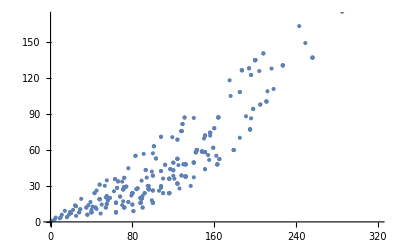

```mathematica
multFreeRings = Cases[ FRL, ring_ /; Mult[ring] == 1 ];
ListPlot[ 
	Table[ { NNZSC[ ring ], TQDS[ ring ] }, { ring, multFreeRings } ]
]
```

Colour the rings according to rank, add labels, and add tooltips

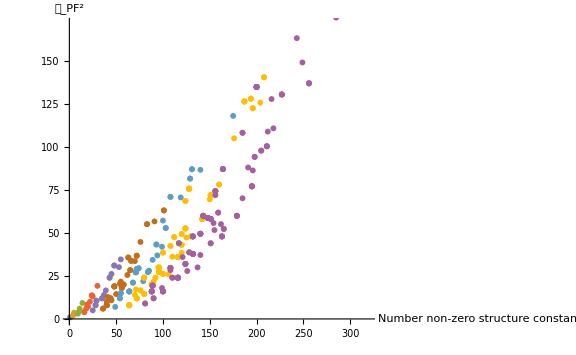

```mathematica
ListPlot[ 
	Table[ Tooltip[{ NNZSC[ ring ], TQDS[ ring ]}, FC[ring] ], { ring, # } ]& /@ GatherBy[ multFreeRings, Rank ],
	PlotLegends -> Table[ "Rank = " <> ToString[i], {i, Max[ Rank /@ multFreeRings ] } ], 
	AxesLabel->{ "Number\nnon-zero\nstructure\nconstants", "𝒟_PF^2" },
	ImageSize->Large
]
```

## Working With Elements

You can call elements either by invoking ring[[el]] where el is either an integer denoting the i’th particle or 
it could be the name of the element itself. The product between two element is invoked by calling 
CenterDot[ ring[[el1]], ring[[el2]] ] or using the infix operator · ( Esc . Esc ).

Multiply two elements of the Ising fusion ring

```mathematica
r = FusionRing[
	"MultiplicationTable" -> {{{1,0,0},{0,1,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,1},{0,0,1},{1,1,0}}}
];
r[[3]]·r[[3]]
```

𝟭+𝟮

or

```mathematica
CenterDot[ r[[2]], r[[3]] ]
```

σ

The product is associative and works for any amount of elements (Or it did. I’ll have to fix this at some point)

```mathematica
CenterDot[r[[3]],r[[3]],r[[1]]+r[[3]],r[[3]]+r[[2]]]
```

𝟭·𝟭+2 𝟭·𝟮+2 𝟭·𝟯+𝟮·𝟭+2 𝟮·𝟮+2 𝟮·𝟯

Calculations can entered in a more readable form using a Block statement

```mathematica
Block[{
	id = r[[1]],
	ψ  = r[[2]],
	σ  = r[[3]]
	},
	( 3 ψ + 2 σ + id )·ψ·( ψ + 3 id )
]//FullForm
```